## Analysis of the metapopulation dynamics

#### This document includes:

Code to generate Figure 3

Code to generate six coexisting strains used for Figure D6 and D7

Code to generate Figure S1

## Functions

### In-patch solvers

```mathematica
(* Default parameters *)
Clear[defaults];
defaults={
sFe->5,
sApo->1,
d->1,
dm->0.1,

kf->1,
γ->3,
vh->10,Kh->1,
ϵ->1.
};

(* In-patch solution *)
a=kf;
b=-(kf (sFe + ϵ α M [t]+ sApo) + d^2);
c=kf sFe ( ϵ α M[t] + sApo);
Qstar = (-b - Sqrt[b^2-4 a c])/(2 a);
(d^2+kf (sApo+sFe+α ϵ M[t])-√(-4 kf^2 sFe (sApo+α ϵ M[t])+(-d^2-kf (sApo+sFe+α ϵ M[t]))^2))/(2 kf);
eq = 0==((1-α)γ vh Qstar/ (vh M[t] + Kh d) -dm )M[t];
0==M[t] (-dm+(vh (1-α) γ (d^2+kf (sApo+sFe+α ϵ M[t])-√(-4 kf^2 sFe (sApo+α ϵ M[t])+(-d^2-kf (sApo+sFe+α ϵ M[t]))^2)))/(2 kf (d Kh+vh M[t])));
numSol=Solve[Evaluate[eq]/.defaults, M[t],NonNegativeReals];

(* M[0] must be found separately *)
Qzero=(kf(sFe+sApo)+d^2-Sqrt[(kf(sFe+sApo)+d^2)^2-4 kf^2 sFe sApo])/(2 kf)/. defaults;
Mzero=(γ vh Qzero-Kh d dm)/(vh dm)/. defaults;

(*Pick the physical (positive real) nontrivial root*)
ClearAll[Biomass]
Biomass[a_?NumericQ]:=(
If[a == 0, Return[Mzero]];
Module[{candidates},candidates=Select[M[t]/. numSol/. α->a,NumericQ[#]&&Im[#]==0&&Re[#]>0&];
If[Length[candidates]==0,0,Re[First[candidates]]]]
)

(* alphahat maximizes biomass *)
alphahat=Module[{x},(x/.FindMaximum[{Biomass[x],0<x<=0.5},x][[2]])];

(* Given an equilibrium biomass, back-calculate the corresponding α value. high = True finds the one >α̂ *)
Clear[Strategy];
Strategy[bio_,high_:False]:=Strategy[bio,high]=Module[{x},(
If[bio>Biomass[alphahat],Return[None]];

If[high,
xmin=alphahat;xmax=1;x0=(alphahat+1)/2;,
xmin=0;xmax=alphahat;x0=alphahat/2;];
Quiet@Check[x/. FindRoot[Biomass[x]==bio,{x,x0,xmin,xmax}],None]
)]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Biomass[0]
Biomass[0.01]
Biomass[0.1]
```

24.1225

30.9406

120.845

```mathematica
Strategy[0]
Strategy[24.122527892982443]
Strategy[30.940638368414]
Strategy[30.940638368414,True]
Strategy[200]
```

None

0.

0.01

0.782947

None

```mathematica
Strategy[Biomass[0]*2]
```

0.0237006

### Metapopulation

```mathematica
(* Generate ODEs for Hastings' formulation of Levins-Culver metapopulation model *)
Clear[GenerateLevins];
GenerateLevins[N_]:=(
Clear[c,p,m];
Table[p[i]'[t] == c[i]*p[i][t]*(1-Sum[p[j][t],{j,i}])-m*p[i][t]-p[i][t]*Sum[c[j]*p[j][t],{j,i-1}],
{i,1,N}])

(* Numerically solve the Levins model for given dispersals, mortality rate, and initial values *)
Clear[SolveLevins];
SolveLevins[dispersals_,mort_,start_:0.1,maxT_:1000]:=Module[
{
size=Length[dispersals],
starts,
endT=maxT,
sol
},
Clear[c,p,m];
starts=If[NumericQ[start],ConstantArray[start,size],start];
If[size!=Length[starts],Print["Vectors are of unequal size!"];Abort[]];
sol=NDSolve[{
GenerateLevins[size] ,
Thread[Array[p[#][0]&,size]==starts]}
/.Thread[Array[c,size]->dispersals]/.m->mort ,
Array[p,size],{t,0,maxT}
];
Association[Append[sol[[1]],"end"->endT]]
];
```

## Representative dynamics (Figure 3)

```mathematica
mortality=Biomass[0]/2;
low=Biomass[0];
med=Biomass[0.03];
high=Biomass[0.1];
```

#### producer reaching equilibrium

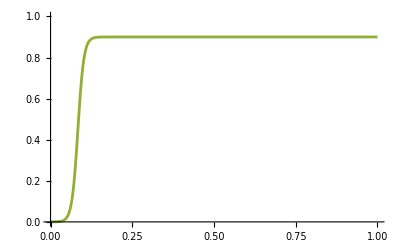

```mathematica
sol1=SolveLevins[{low,med,high}, mortality, {0, 0, 0.0001}];
t1=1;
Plot[Evaluate[{None[t],None[t],p[3][t]}/.sol1], {t,0,t1},PlotRange->{0,1}]
```

### partial cheater invades

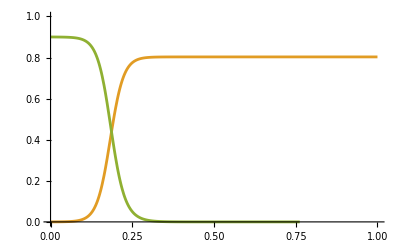

```mathematica
sol2=SolveLevins[{low,med,high}, mortality, {p[1][t],0.0001,p[3][t]}/.t->t1/.sol1];
t2=1;
Plot[Evaluate[{None[t],p[2][t],p[3][t]}/.sol2], {t,0,t2},PlotRange->{0,1}]
```

### total cheater invades

```mathematica
sol3=SolveLevins[{low,med,high}, mortality, {0.001,p[2][t],0}/.t->t2/.sol2];
t3=1.5;
Plot[Evaluate[{p[1][t],p[2][t],None[t]}/.sol3], {t,0,t3},PlotRange->{0,1},PlotLabels->{"zero","mid", "high"}]
```

-Graphics-

### producer can now invade

```mathematica
sol4=SolveLevins[{low,med,high}, mortality, {p[1][t],p[2][t],0.001}/.t->t3/.sol3];
t4=1.5;
Plot[Evaluate[{p[1][t],p[2][t],p[3][t]}/.sol4], {t,0,t4},PlotRange->{0,1},PlotLabels->{"zero","mid", "high"}]
```

-Graphics-

### Combined plot

```mathematica
end1=t1;
end2=end1+t2;
end3=end2+t3;
end4=end3+t4;
combo[t]={
Piecewise[{
{None[t]/.sol1, t<=end1},
{None[t-end1]/.sol2,end1<t<=end2},
{p[1][t-end2]/.sol3,end2<t<=end3},
{p[1][t-end3]/.sol4,end3<t<=end4}
}],
Piecewise[{
{None[t]/.sol1, t<=end1},
{p[2][t-end1]/.sol2,end1<t<=end2},
{p[2][t-end2]/.sol3,end2<t<=end3},
{p[2][t-end3]/.sol4,end3<t<=end4}
}],
Piecewise[{
{p[3][t]/.sol1, t<=end1},
{p[3][t-end1]/.sol2,end1<t<=end2},
{None[t-end2]/.sol3,end2<t<=end3},
{p[3][t-end3]/.sol4,end3<t<=end4}
}]
};
```

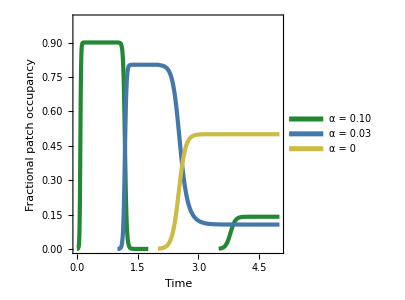

```mathematica
colors={RGBColor["#228833"],RGBColor["#4477AA"],RGBColor["#CCBB44"]};
legend=Reverse[{"α = 0","α = 0.03","α = 0.10"}];
Plot[Evaluate[Reverse[combo[t]]],{t,0,end4}, PlotRange->{0,1},
PlotStyle->Map[Directive[#,Thickness[0.01]]&,colors],
Frame->True,FrameLabel->{"Time","Fractional patch occupancy"},
PlotLegends->Placed[LineLegend[Map[Directive[#,Thickness[0.01]]&,colors],legend],{0.7,0.85}],
BaseStyle->Directive[FontSize->14,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],
ImageSize->{300,300},AspectRatio->1,
FrameTicks->{{Automatic, None},{Automatic,None}}
]
```

## Niche shadow plot generation (Figure 3B)

```mathematica
alphamin=0;
alphamax=1;
FindEq[strains_, mortality_]:=Module[
{
strats=Sort[strains],
threshold=mortality,
survivors={},
freqs={},
biomasses = {},
shadowthresholds={},
invaderregion={},
shadowregion={},
c,freq,newthresh,strat
},(
Do[
c = Biomass[strats[[i]]];
If[c > threshold, (
freq = 1-Total[freqs]-mortality/c-Sum[biomasses[[j]]*freqs[[j]],{j,Length[biomasses]}]/c;
AppendTo[survivors,strats[[i]]];
AppendTo[biomasses,c];
AppendTo[freqs, freq];
strat=Strategy[Sqrt[c*threshold]];
If[strat===None,strat=alphamin];
AppendTo[invaderregion,{strat,strats[[i]]}];
threshold=c^2/threshold;
AppendTo[shadowthresholds,threshold];
strat=Strategy[threshold];
If[strat===None,strat=alphamax];
AppendTo[shadowregion,{strats[[i]],strat}];
strat=Strategy[threshold, True]; (* Also get high strat shadow *)
If[strat===None,Null,AppendTo[shadowregion,{strat,alphamax}]];
)];
,{i, Length[strains]}];
<|"strains"->survivors,"freqs"->freqs,"biomasses"->biomasses, "mortality" ->mortality,
"shadow_threshold"->shadowthresholds,"replaced_by"->invaderregion,"replaces"->shadowregion|>
)]
```

```mathematica
FindEq[{0.01},Biomass[0]/2]
```

<|strains→{0.01},freqs→{0.610181},biomasses→{30.9406},mortality→12.0613,shadow_threshold→{79.3717},replaced_by→{{0,0.01}},replaces→{{0.01,0.037504},{0.453716,1}}|>

```mathematica
FindEq[{0,0.03, 0.1}, Biomass[0]/2]
```

<|strains→{0,0.03,0.1},freqs→{0.5,0.106214,0.140329},biomasses→{24.1225,61.2579,120.845},mortality→12.0613,shadow_threshold→{48.2451,77.7807,187.752},replaced_by→{{0,0},{0.0268704,0.03},{0.0464485,0.1}},replaces→{{0,0.0237006},{0.666318,1},{0.03,0.0368314},{0.464719,1},{0.1,1}}|>

```mathematica
ClearAll[ShadowPlot];
ShadowPlot[status_,ymin_:0.05,ymax_:0.85]:=Module[{
x=0.02*(ymax-ymin),
tip=0.075*(ymax-ymin),
spacer=0.005*(ymax-ymin),
strains,shadows,replaced
},
(
strains=Map[Disk[{0,#},x*0.25]&,status["strains"]];
shadows=Map[If[#[[1]]<ymax,Rectangle[{-x,#[[1]]},{x,Min[#[[2]],ymax]}],Nothing]&,status["replaces"]];
replaced=Map[Rectangle[{-x,Max[#[[1]],ymin]},{x,Min[ymax,#[[2]],1]}]&,status["replaced_by"]];

Show[
(* landmarks *)
Graphics[{Black, 
If[ymin===0,
{Line[{{x,0},{tip,0}}],Text["0",{tip+spacer,0},{Left,Center}]},
{Line[{{tip,ymin},{x,ymin}}],Text[ymin,{tip+spacer,ymin-spacer},{Left,Center}]}
],
If[ymax===1,
{Line[{{x,1},{tip,1}}],Text["1",{tip+spacer,1},{Left,Center}]},
{Line[{{tip,ymax},{x,ymax}}],Text[ymax,{tip+spacer,ymax+spacer},{Left,Center}]}
],
If[alphamin!=0,
{Line[{{x,alphamin},{tip,alphamin}}],Text["α_min",{tip+spacer,alphamin+spacer},{Left,Center}]},
Nothing
],
Line[{{x,alphahat},{tip,alphahat}}],Text["α̂",{tip+spacer,alphahat},{Left,Center}],
Line[{{x,alphamax},{tip,alphamax}}],Text["α_max",{tip+spacer,alphamax+spacer},{Left,Center}],
If[ymax===1,Line[{{x,1},{tip,1}}],Text["1",{tip+spacer,1},{Left,Center}],Nothing]
}],
(* shadows *)
Graphics[{RGBColor["#EE99AA"],shadows}],
(* dead by mortality *)
If[!Strategy[status["mortality"]]===None,
Graphics[{RGBColor["#777777"], 
Rectangle[{-x,ymin},{x,Strategy[status["mortality"]]}],
Rectangle[{-x,Min[ymax,Strategy[status["mortality"],True]]},{x,ymax}]}],
Graphics[]
],
(* dead by ODEs *)
Graphics[{RGBColor["#777777"], 
If[ymin<alphamin,Rectangle[{-x,ymin},{x,alphamin}],Nothing],
If[ymax>alphamax,Rectangle[{-x,alphamax},{x,ymax}],Nothing]}],
(* Number line *)
Graphics[Line[{{0,ymin},{0,ymax}}]],
If[ymax!=1,Graphics[{Dashed,Line[{{0,ymax},{0,ymax+x}}]}],Graphics[]],
If[ymin!=0,Graphics[{Dashed,Line[{{0,ymin},{0,ymin-x}}]}],Graphics[]],
(* strain dots *)
Graphics[{FaceForm[White],EdgeForm[Black],strains}],
(* Control the dimensions *)
Graphics[Line[{{-x,ymax+1.5*x},{4*x,ymax+1.5*x}}]],

BaseStyle->{FontFamily->"Arial"},
PlotRange->{All,{ymin-x,ymax+2*x}},
ImageSize->{70,Automatic}
]
)]
```

```mathematica
mortality=Biomass[0]/2;
low = 0; high = 0.3;
strains={0.1};
status=FindEq[strains,mortality]
ShadowPlot[status,low,high]
```

<|strains→{0.1},freqs→{0.900192},biomasses→{120.845},mortality→12.0613,shadow_threshold→{1210.78},replaced_by→{{0.0169887,0.1}},replaces→{{0.1,1}}|>

-Graphics-

### Figure 3B

```mathematica
mortality=Biomass[0]/2;
low = 0; high = 0.15;

GraphicsRow[{
ShadowPlot[FindEq[{0.1},mortality],low,high],
ShadowPlot[FindEq[{0.03, 0.1},mortality],low,high],
ShadowPlot[FindEq[{0,0.03},mortality],low,high],
ShadowPlot[FindEq[{0,0.03,0.1},mortality],low,high],
}]
```

-Graphics-

## Calculating a scenario where many strains coexist

#### six strains at 0.1

```mathematica
Clear[GenerateLevinsEq];
GenerateLevinsEq[N_]:=(
Clear[c,p,m];
Table[0 == c[i]*p[i]*(1-Sum[p[j],{j,i}])-m*p[i]-p[i]*Sum[c[j]*p[j],{j,i-1}],
{i,1,N}])
sixstrain =GenerateLevinsEq[6]
```

{0==-m p[1]+c[1] (1-p[1]) p[1],0==-m p[2]-c[1] p[1] p[2]+c[2] (1-p[1]-p[2]) p[2],0==-m p[3]-(c[1] p[1]+c[2] p[2]) p[3]+c[3] (1-p[1]-p[2]-p[3]) p[3],0==-m p[4]-(c[1] p[1]+c[2] p[2]+c[3] p[3]) p[4]+c[4] (1-p[1]-p[2]-p[3]-p[4]) p[4],0==-m p[5]-(c[1] p[1]+c[2] p[2]+c[3] p[3]+c[4] p[4]) p[5]+c[5] (1-p[1]-p[2]-p[3]-p[4]-p[5]) p[5],0==-m p[6]-(c[1] p[1]+c[2] p[2]+c[3] p[3]+c[4] p[4]+c[5] p[5]) p[6]+c[6] (1-p[1]-p[2]-p[3]-p[4]-p[5]-p[6]) p[6]}

```mathematica
target = sixstrain/.Map[p[#]->0.1&,{1,2,3,4,5,6}]/.{c[1]->Biomass[0]}
```

{0==2.17103-0.1 m,0==-0.241225-0.1 m+0.08 c[2],0==-0.1 m-0.1 (2.41225+0.1 c[2])+0.07 c[3],0==-0.1 m-0.1 (2.41225+0.1 c[2]+0.1 c[3])+0.06 c[4],0==-0.1 m-0.1 (2.41225+0.1 c[2]+0.1 c[3]+0.1 c[4])+0.05 c[5],0==-0.1 m-0.1 (2.41225+0.1 c[2]+0.1 c[3]+0.1 c[4]+0.1 c[5])+0.04 c[6]}

```mathematica
solution=Flatten[{c[1]->Biomass[0],NSolve[target, {c[2],c[3],c[4],c[5],c[6],m}][[1]]}]
```

{c[1]→24.1225,c[2]→30.1532,c[3]→38.7683,c[4]→51.6911,c[5]→72.3676,c[6]→108.551,m→21.7103}

```mathematica
strains = Map[Strategy[#[[2]]]&,solution[[1;;6]]]
```

{0.,0.00906048,0.0174581,0.0255439,0.0345996,0.0566182}

```mathematica
mortality=m/.solution;
low = 0; high = 0.15;
strains=strains;
status=FindEq[strains,mortality]
ShadowPlot[status,low,high]
```

<|strains→{0.,0.00906048,0.0174581,0.0255439,0.0345996,0.0566182},freqs→{0.1,0.1,0.1,0.1,0.1,0.1},biomasses→{24.1225,30.1532,38.7683,51.6911,72.3676,108.551},mortality→21.7103,shadow_threshold→{26.8028,33.9223,44.3067,60.3063,86.8411,135.689},replaced_by→{{0,0.},{0.00683679,0.00906048},{0.0153793,0.0174581},{0.0234818,0.0255439},{0.0320229,0.0345996},{0.0465402,0.0566182}},replaces→{{0.,0.00449827},{0.810679,1},{0.00906048,0.0131975},{0.76292,1},{0.0174581,0.0213563},{0.692942,1},{0.0255439,0.0295873},{0.584467,1},{0.0345996,0.0408641},{0.401721,1},{0.0566182,1}}|>

-Graphics-

#### six strains all equal abundance, including 0 and alpha_hat

```mathematica
Clear[GenerateLevinsEq];
GenerateLevinsEq[N_]:=(Clear[c,p,m];
Table[0==c[i]*p[i]*(1-Sum[p[j],{j,i}])-m*p[i]-p[i]*Sum[c[j]*p[j],{j,i-1}],{i,1,N}])
sixstrain=GenerateLevinsEq[6];

target=sixstrain/. Map[p[#]->pVal&,Range[6]]/. {c[1]->Biomass[0],c[6]->Biomass[alphahat]};

unknowns={c[2],c[3],c[4],c[5],m,pVal};

solution=NSolve[target,unknowns]
```

{{c[2]→49.3527,c[3]→157.558,c[4]→-3431.49,c[5]→2877.56,m→17.9566,pVal→0.255611},{c[2]→49.3527,c[3]→157.558,c[4]→-3431.49,c[5]→2877.56,m→17.9566,pVal→0.255611},{c[2]→49.3527,c[3]→157.558,c[4]→-3431.49,c[5]→2877.56,m→17.9566,pVal→0.255611},{c[2]→-56.3947-137.306 ⅈ,c[3]→-37.715+69.8654 ⅈ,c[4]→63.5616-90.1014 ⅈ,c[5]→-21.4433-135.696 ⅈ,m→-27.9634-37.6748 ⅈ,pVal→0},{c[2]→30.4894,c[3]→39.7602,c[4]→54.0176,c[5]→77.6189,m→21.6039,pVal→0.104411}}

```mathematica
solution=solution[[5]]
```

{c[2]→30.4894,c[3]→39.7602,c[4]→54.0176,c[5]→77.6189,m→21.6039,pVal→0.104411}

```mathematica
mortality=m/.solution;
low = 0; high = 0.15;
strains=Flatten[{0, Map[Strategy[#[[2]]]&,solution[[1;;4]]], alphahat}];
status=FindEq[strains,mortality]
ShadowPlot[status,low,high]
```

<|strains→{0,0.00946707,0.0182204,0.026703,0.0367635,0.109132},freqs→{0.104411,0.104411,0.104411,0.104411,0.104411,0.104411},biomasses→{24.1225,30.4894,39.7602,54.0176,77.6189,121.012},mortality→21.6039,shadow_threshold→{26.9348,34.5131,45.8051,63.7025,94.5755,154.838},replaced_by→{{0,0},{0.00714547,0.00946707},{0.016052,0.0182204},{0.024522,0.026703},{0.0337646,0.0367635},{0.0547962,0.109132}},replaces→{{0,0.00469799},{0.809796,1},{0.00946707,0.0137723},{0.758948,1},{0.0182204,0.0222828},{0.682818,1},{0.026703,0.0310401},{0.56132,1},{0.0367635,0.0449734},{0.347058,1},{0.109132,1}}|>

-Graphics-

#### six strains all equal abundance, including alpha_hat, with mu = delta(0)

```mathematica
Clear[GenerateLevinsEq];
GenerateLevinsEq[N_]:=(Clear[c,p,m];
Table[0==c[i]*p[i]*(1-Sum[p[j],{j,i}])-m*p[i]-p[i]*Sum[c[j]*p[j],{j,i-1}],{i,1,N}])
sixstrain=GenerateLevinsEq[6];

target=sixstrain/. Map[p[#]->pVal&,Range[6]]/. {m->Biomass[0],c[6]->Biomass[alphahat]};

unknowns={c[1],c[2],c[3],c[4],c[5],pVal};

solution=NSolve[target,unknowns]
```

{{c[1]→32.8884,c[2]→70.4354,c[3]→257.799,c[4]→-1820.03,c[5]→1096.35,pVal→0.266535},{c[1]→32.8884,c[2]→70.4354,c[3]→257.799,c[4]→-1820.03,c[5]→1096.35,pVal→0.266535},{c[1]→32.8884,c[2]→70.4354,c[3]→257.799,c[4]→-1820.03,c[5]→1096.35,pVal→0.266535},{c[1]→32.8884,c[2]→70.4354,c[3]→257.799,c[4]→-1820.03,c[5]→1096.35,pVal→0.266535},{c[1]→26.8067,c[2]→33.5195,c[3]→43.1146,c[4]→57.5177,c[5]→80.5857,pVal→0.100132},{c[1]→114.331+35.874 ⅈ,c[2]→-28.846-91.3057 ⅈ,c[3]→39.8504+99.1787 ⅈ,c[4]→89.2468-62.8828 ⅈ,c[5]→10.1409-76.2794 ⅈ,pVal→0}}

```mathematica
solution=solution[[5]]
```

{c[1]→26.8067,c[2]→33.5195,c[3]→43.1146,c[4]→57.5177,c[5]→80.5857,pVal→0.100132}

```mathematica
mortality=Biomass[0];
low = 0; high = 0.15;
strains=Flatten[{Map[Strategy[#[[2]]]&,solution[[1;;5]]], alphahat}];
status=FindEq[strains,mortality]
ShadowPlot[status,low,high]
```

<|strains→{0.00450425,0.0127954,0.0205846,0.028346,0.0380249,0.109132},freqs→{0.100132,0.100132,0.100132,0.100132,0.100132,0.100132},biomasses→{26.8067,33.5195,43.1146,57.5177,80.5857,121.012},mortality→24.1225,shadow_threshold→{29.7896,37.7163,49.2854,67.1251,96.7454,151.365},replaced_by→{{0.002305,0.00450425},{0.0107533,0.0127954},{0.0186407,0.0205846},{0.0263236,0.028346},{0.0350815,0.0380249},{0.0561928,0.109132}},replaces→{{0.00450425,0.00861146},{0.790669,1},{0.0127954,0.0166133},{0.737392,1},{0.0205846,0.024275},{0.659277,1},{0.028346,0.0324606},{0.53794,1},{0.0380249,0.0463159},{0.331503,1},{0.109132,1}}|>

-Graphics-

## PIPs

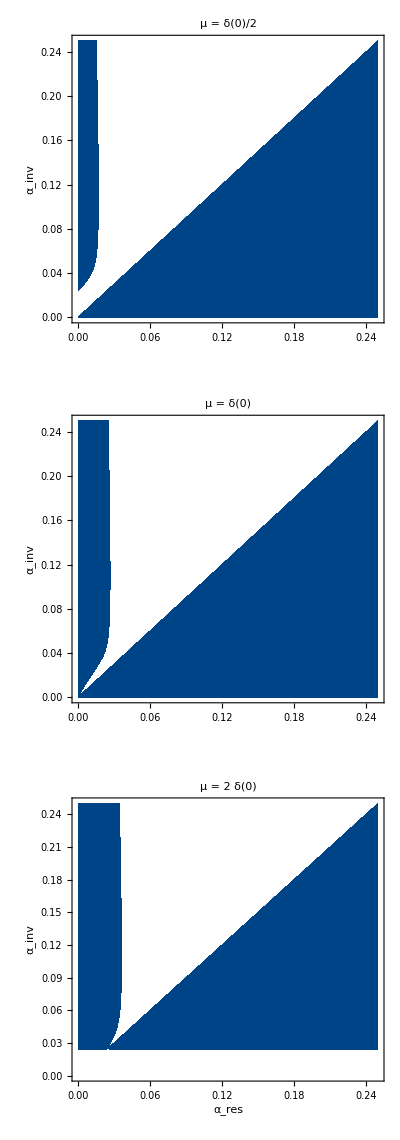

```mathematica
m = Biomass[0]/2;
windowmax=0.25;
plt1=RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},(α2<α1|| inv>res^2/m)&&inv>m],{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,BoundaryStyle->None,PlotStyle->RGBColor["#004488"],FrameLabel->{None,"α_inv"},PlotLabel->"μ = δ(0)/2"];
m = Biomass[0];
plt2=RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},(α2<α1|| inv>res^2/m)&&inv>m],{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,BoundaryStyle->None,PlotStyle->RGBColor["#004488"],FrameLabel->{None,"α_inv"},PlotLabel->"μ = δ(0)"];
m = Biomass[0]*2;
plt3=RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},(α2<α1|| inv>res^2/m)&&inv>m],{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,BoundaryStyle->None,PlotStyle->RGBColor["#004488"],FrameLabel->{"α_res","α_inv"},PlotLabel->"μ = 2 δ(0)"];
GraphicsColumn[{plt1,plt2,plt3}]
```

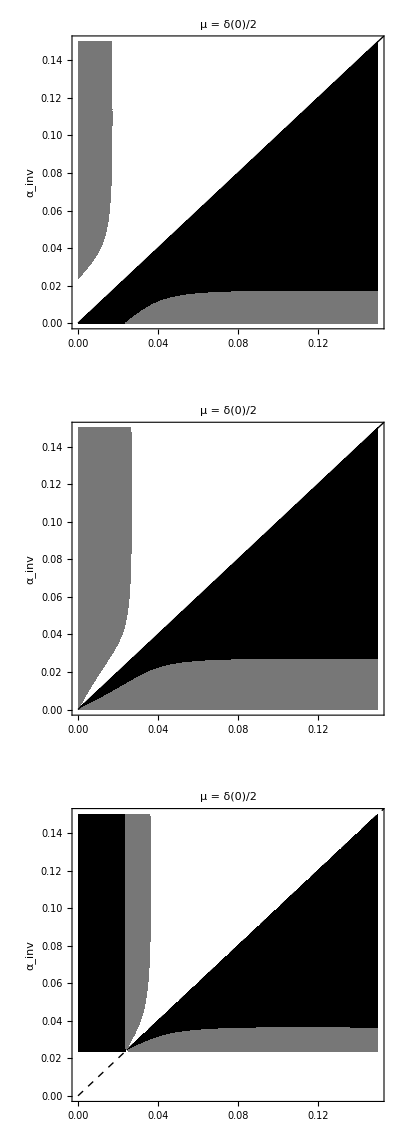

```mathematica
m = Biomass[0]/2;
windowmax=0.15;
plt1=Show[
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},inv>m &&(α2<α1||res<m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#000000"],FrameLabel->{None,"α_inv"},PlotLabel->"μ = δ(0)/2",
Epilog->{Black, Line[{{0,0},{1,1}}] }
],
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},res>m && inv > m && (res>inv^2/m||inv>res^2/m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#777777"]]
];
m = Biomass[0];
plt2=Show[
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},inv>m && (α2<α1||res<m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#000000"],FrameLabel->{None,"α_inv"},PlotLabel->"μ = δ(0)/2",
Epilog->{Black, Line[{{0,0},{1,1}}] }
],
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},res>m && inv > m && (res>inv^2/m||inv>res^2/m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#777777"]]
];
m = Biomass[0]*2;
plt3=Show[
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},inv>m && (α2<α1||res<m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#000000"],FrameLabel->{None,"α_inv"},PlotLabel->"μ = δ(0)/2",
Epilog->{Directive[Dashed,Black], Line[{{0,0},{1,1}}] }
],
RegionPlot[With[{res=Biomass[α1],inv=Biomass[α2]},res>m && inv > m && (res>inv^2/m||inv>res^2/m)],
{α1,0,windowmax},{α2,0,windowmax},PlotPoints->50,PlotRangePadding->None,
BoundaryStyle->None,PlotStyle->RGBColor["#777777"]]
];
GraphicsColumn[{plt1,plt2,plt3}]
```